```mathematica
ClearAll["Global`*"]
```

```mathematica
<<ExaminePareto`
```

## AverageRatioBiggerThanMax

3.1. PercentsBiggerThanMax tells us how many values bigger than the initial max we get. But it doesn’t tell us how much bigger those values are. Now lets introduce a new metric 'AverageRatioBiggerThanMax'. Here we ask, when a new value is bigger than the initial-max we have seen so far, how much bigger is it and we average this for the experiment. The histogram shows us that values that are bigger are usually around twice as big for shape=1.5 and when initial samples is 40. Note: You can see a bar at 0 which might seem unexpected. The reason this is there is because the metric also counts experiments where there were no trials which produced values greater than the initial max. In this case there were very few experiments where no values bigger than the initial-max were found.

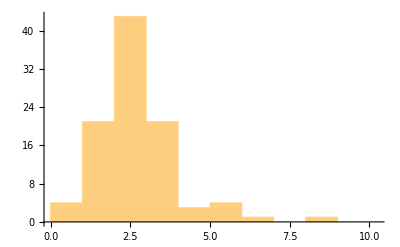

```mathematica
Histogram[AverageRatioBiggerThanMax[1.5,100,1000]]
```

3.2. Lets see how this metric behaves as we change the number of initial samples. Remember for PercentsBiggerThanMax everything got really bunched up to 0 as the number of initial samples went up. What we see at 0 is that as the number of experiments where we see no new maxes goes up (as we’d expect). Obviously any zero-cases have to come out of the rest of the histogram for that slice and we can see that the metric does bunch up slightly towards 1 as samples increases.

```mathematica
ForRangeSamplesHistogram3D[AverageRatioBiggerThanMax,
200,
50,500,50,
1.0, 
1000,
 {0,10,0.1},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.3. Lets see what happens to AverageRatioBiggerThanMax as we vary the value of shape. At the finer resolution we see that with very low values of shape we see

```mathematica
ForRangeShapeHistogram3D[AverageRatioBiggerThanMax,200,0.1,2,0.1,
1000,
40,Automatic, ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.4. Oh, that's a problem. We see that for a low value of shape we get a small amount of very high ratios .. (probably because the initial max was so low). Mathematica can't do a very good job of showing us what really happened. Lets try it again but give it hints as to how to do the histogram. Below we can see that for very low values of shape that this metric is going to give very sparse and high results (in fact we can hardly see any). It does seem that as the shape variable increases this metric shrinks up around one.

```mathematica
ForRangeShapeHistogram3D[AverageRatioBiggerThanMax,200,0.1,2,0.1,
1000,
40,
{0,10,0.1}, 
ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

## DiffBetweenVarAndMaxCalc

3.5.Lets introduce another metric 'DiffBetweenVarAndMaxCalc'. Here we aim to visualise what all the differences (positive and negative) are between the newly drawn values and the initial max. The data that fills the histogram is the difference of every new value with the initial max for every experiment. The Histogram below shows us that most of the new values drawn are slightly below the initial max.

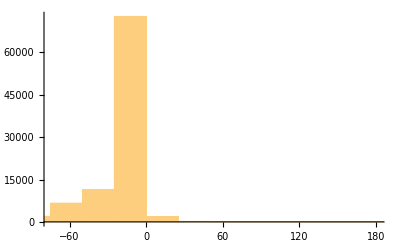

```mathematica
Histogram[DiffBetweenVarAndMaxCalc[1.5,100,1000]]
```

3.6. Lets vary the number of initial values (z axis) and see how it affects the histogram. First lets see how Mathematica does on its own without specifying the range and the width of the histogram bars. It doesn’t do so well because of a far outlier.

```mathematica
ForRangeSamplesOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
50,500,50,
1.0, 
1000, 
Automatic,ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.7. Lets specify the range and see whats happening around zero. As the initial sample size increases the diffs spread out and fall back from zero.

```mathematica
ForRangeSamplesOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
50,500,50,
1.0, 
1000, 
{-4000,4000,20},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.8. And an even more zoomed in view.

```mathematica
ForRangeSamplesOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
50,500,50,
1.0, 
1000, 
{-2000,500,10},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.9. Now lets see what happens to DiffBetweenVarAndMaxCalc as we vary shape.

```mathematica
ForRangeShapeOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
0.1,2,0.1,
1000, 
40, 
{-2000,500,10},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

```mathematica
ForRangeShapeOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
0.1,2,0.1, 
1000, 40, {-200,100,1},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

```mathematica
ForRangeShapeOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
0.1,2,0.1,
1, 
40, 
{-1000,30,1},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

3.10 Lets vary the range of samples for the DiffBetweenVarAndMaxCalc metric. Here are 2 histograms. So here what we see is that as initial sample size increases the differences between the initial-max and the newly drawn values don't cluster so much around 0. Also it is clear again that as the sample size increases there are less 'surprise' values over the initial max.

```mathematica
ForRangeSamplesOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
10,200,10,
1.0, 
1000, {-200,100,1},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

```mathematica
ForRangeSamplesOverTrialsHistogram3D[DiffBetweenVarAndMaxCalc,
200,
10,200,10,
1.0, 
1000, {-500,500,1},ChartElementFunction->"GradientScaleCube"]
```

-Graphics3D-

## CHANGING SUBSEQUENT TRIALS

3.11. We know that changing the number of initial samples affects the likelihood of us seeing values far in excess of what we have already seen. In this Histogram we do something that is obvious just to set up some of our further work. Here in the z axis we vary the number of subsequent trials we do for each experiment (i.e. the number of values we take for X after the initial 40). As we would expect varying the trials has little effect on the probabilities of us seeing values bigger than the initial max. Whether we run 100 trials or 2000 trials the probabilities are the same.

```mathematica
ForRangeHistogram3D[PercentsBiggerThanMax, 100,500,2000,500,1.5,]
```

-Graphics3D-

3.12. Now we do something similar to (3.11) for AverageRatioBiggerThanMaxand we can see that as we vary the number of subsequent trials the metric doesn't seem to change. We do see that as there are more trials in an experiment the number of 0 counts should go down.

```mathematica
ForRangeHistogram3D[AverageRatioBiggerThanMax,100,500,2000,500,1.5]
```

-Graphics3D-

3.13. Similar to (3.11) and (3.12) here we look at how varying the subsequent trials (in the z axis) affects what we see in the Histogram. As in this case we get a result for each trial not just per experiment we can see that the total size of all the histogram bars increases in the z axis as we would expect. In effect, each subsequent x/y histogram contains the information of the previous histogram and adds more.

```mathematica
ForRangeTrialsHistogram3D[DiffBetweenVarAndMaxCalc,200,500,4000,500,1.5, {-100,100,1}]
```

-Graphics3D-